```mathematica
data={{0.4,0.25},{0.45,0.45},{0.5,0.95},{0.55,1.2},{0.6,1.6},{0.65,2.10},{0.7,2.6}}
```

{{0.4,0.25},{0.45,0.45},{0.5,0.95},{0.55,1.2},{0.6,1.6},{0.65,2.1},{0.7,2.6}}

```mathematica
ArrayPlot[data]
```

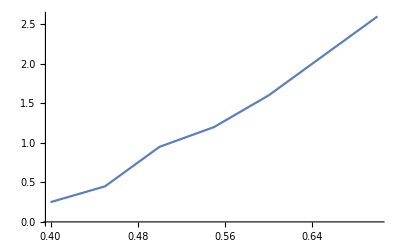

```mathematica
ListPlot[data,Joined->True]
```

```mathematica
Fit[data, {1,x,x^2,x^3},x]
```

-2.24881+8.31746 x-9.7619 x^2+11.1111 x^3

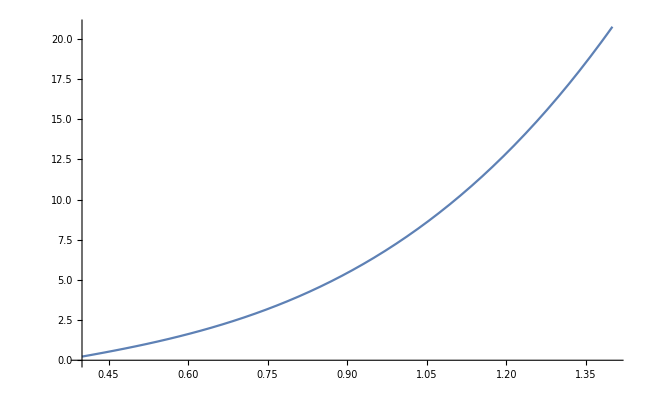

```mathematica
Plot[-2.248809523809392+8.317460317459625 x-9.761904761903557 x^2+11.11111111111043 x^3,{x,0.4,1.4}]
```

```mathematica
Function[x,E^(-2Pi/x)]
```

Function[x,ⅇ^(-(2 π)/x)]

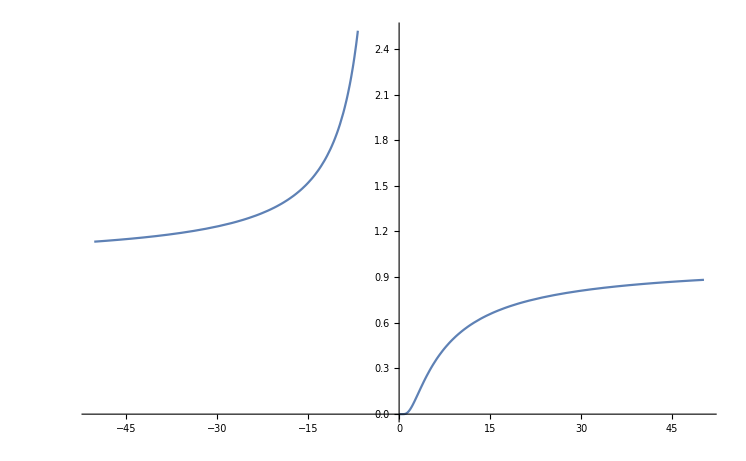

```mathematica
Plot[Function[x,ⅇ^(-(2 π)/x)][x],{x,-16 π,16 π}]
```

```mathematica
Function[x,u*((2Pi*2.998*10^14)/x)^2*E^((-2Pi*2.998*10^14)/x)]
```

Function[x,u ((2 π 2.998 10^14)/x)^2 ⅇ^(-(2 π 2.998 10^14)/x)]

```mathematica
Function[x,(9*(2Pi/x)^3)*(((2Pi*2.998*10^14)/x)^2)*((85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))*(√(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))]
```

Function[x,((9 ((2 π)/x)^3) ((2 π 2.998 10^14)/x)^2 (85.3389 x^2-1853.23 x^4+16.5164 x^6) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))/(-0.495117+36.4408 x^2-474.677 x^4+x^6)]

```mathematica
Simplify[((9 ((2 π)/x)^3) ((2 π 2.998 10^14)/x)^2 (85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)]
```

```mathematica
(1.3083396419865956*^35 (5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))/(x^3 (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))(*分母*)
```

```mathematica
Simplify[u ((2 π 2.998 10^14)/x)^2 ⅇ^(-(2 π 2.998 10^14)/x)]
```

(3.54832×10^30 ⅇ^(-1.8837×10^15/x) u)/x^2

```mathematica
Simplify[((3.5483217534163504*^30 ⅇ^(-1.88369895509244*^15/x) u)/x^2)/((1.3083396419865956*^35 (5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))/(x^3 (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))]
```

```mathematica
(0.000027120799825560157 ⅇ^(-1.88369895509244*^15/x) u x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))             (*kaolvyixiadanwei*)
```

```mathematica
Manipulate[Plot[%7,{x,0.4,0.7}],{u,-8,8}]
```

General::unfl: Underflow occurred in computation.

```mathematica
Plot[(0.000027120799825560157 ⅇ^(-1.88369895509244/x) * x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)*10^500)/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))),{x,0.4,5}]
```

-Graphics-

General::unfl: Underflow occurred in computation.

```mathematica
F[y_,m_]:=y-(2Pi*2.998*10^17)/(m*Tan[m])
ContourPlot[F[y_,m_]==0,{y,400,700},{m,0,1000}]
```

-Graphics-

```mathematica
U[g_]:=g*Tan[g]
```

```mathematica
Function[g,g Tan[g]]
```

Function[g,g Tan[g]]

```mathematica
Plot[Function[g,2Pi*10^17/(g Tan[g])][x],{x,-18.84955592153876,18.84955592153876}]
```

-Graphics-

```mathematica
G[x_]:=Arg[x/G]
```

```mathematica
Function[x,Arg[x/G]]
```

Function[x,Arg[x/G]]

```mathematica
Function[x,Arg[x/G]][600]
```

Sum::div: Sum does not converge.

```mathematica
BesselJ[1,5.52]
```

-0.34027

```mathematica
Function[x,(3.7262912531793 ⅇ^(0.116847820014274/x) x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))]
```

Function[x,(3.72629 ⅇ^(0.116848/x) x (-0.495117+36.4408 x^2-474.677 x^4+x^6))/((5.16692-112.205 x^2+1. x^4) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))]

```mathematica
(3.7262912531793 ⅇ^(0.116847820014274/x) x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))
```

(3.72629 ⅇ^(0.116848/x) x (-0.495117+36.4408 x^2-474.677 x^4+x^6))/((5.16692-112.205 x^2+1. x^4) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))

```mathematica
∂_x %147
```

-(1.86315 ⅇ^(0.116848/x) x (-0.495117+36.4408 x^2-474.677 x^4+x^6) ((170.678 x-7412.91 x^3+99.0984 x^5)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)-((72.8817 x-1898.71 x^3+6 x^5) (85.3389 x^2-1853.23 x^4+16.5164 x^6))/((-0.495117+36.4408 x^2-474.677 x^4+x^6)^2)))/((5.16692-112.205 x^2+1. x^4) (1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6))^(3/2))+(3.72629 ⅇ^(0.116848/x) x (72.8817 x-1898.71 x^3+6 x^5))/((5.16692-112.205 x^2+1. x^4) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))-(3.72629 ⅇ^(0.116848/x) x (-224.411 x+4. x^3) (-0.495117+36.4408 x^2-474.677 x^4+x^6))/((5.16692-112.205 x^2+1. x^4)^2 √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))+(3.72629 ⅇ^(0.116848/x) (-0.495117+36.4408 x^2-474.677 x^4+x^6))/((5.16692-112.205 x^2+1. x^4) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))-(0.435409 ⅇ^(0.116848/x) (-0.495117+36.4408 x^2-474.677 x^4+x^6))/(x (5.16692-112.205 x^2+1. x^4) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))

```mathematica
Simplify[%148]
```

(ⅇ^(0.116848/x) (0.0155886-0.133409 x-6.46737 x^2+46.1978 x^3+885.122 x^4-9319.96 x^5-57443.4 x^6+820875. x^7+1.98601×10^6 x^8-3.4545×10^7 x^9-3.76188×10^7 x^10+7.55481×10^8 x^11+3.68963×10^8 x^12-8.38854×10^9 x^13-1.4689×10^9 x^14+3.7631×10^10 x^15+3.02385×10^7 x^16-5.37512×10^8 x^17-205951. x^18+2.89827×10^6 x^19+520.078 x^20-9377.77 x^21-0.435409 x^22+11.1789 x^23))/(x (5.16692-112.205 x^2+1. x^4)^2 (-0.495117+36.4408 x^2-474.677 x^4+x^6) (-0.0282659+6.95232 x^2-132.899 x^4+1. x^6) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))

```mathematica
Cancel[%149]
```

(11.1789 ⅇ^(0.116848/x) (0.00139447-0.0119341 x-0.578535 x^2+4.1326 x^3+79.1781 x^4-833.712 x^5-5138.56 x^6+73430.9 x^7+177658. x^8-3.0902×10^6 x^9-3.36517×10^6 x^10+6.75811×10^7 x^11+3.30054×10^7 x^12-7.50392×10^8 x^13-1.314×10^8 x^14+3.36626×10^9 x^15+2.70497×10^6 x^16-4.80828×10^7 x^17-18423.2 x^18+259263. x^19+46.5232 x^20-838.884 x^21-0.0389493 x^22+1. x^23))/(x (5.16692-112.205 x^2+1. x^4)^2 (-0.495117+36.4408 x^2-474.677 x^4+x^6) (-0.0282659+6.95232 x^2-132.899 x^4+1. x^6) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))

```mathematica
Function[x,(3.7262912531793 ⅇ^(0.116847820014274/x) x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))]
Function[x,(ⅇ^(0.116847820014274/x) (0.015588591238890784-0.13340934590809223 x-6.467372956916895 x^2+46.19782759947689 x^3+885.1220365723125 x^4-9319.960034168205 x^5-57443.36574325667 x^6+820875.2357290179 x^7+1.9860127880391886*^6 x^8-3.454499271858802*^7 x^9-3.7618828226199694*^7 x^10+7.554807891116797*^8 x^11+3.689632697908769*^8 x^12-8.388540231321071*^9 x^13-1.4689031595992975*^9 x^14+3.763097199843844*^10 x^15+3.0238472650059205*^7 x^16-5.375117248494613*^8 x^17-205950.7075777873 x^18+2.8982736048942916*^6 x^19+520.0775090113308 x^20-9377.774385177327 x^21-0.4354090096722584 x^22+11.178873759537902 x^23))/(x (5.166916072738272-112.20528246809232 x^2+1. x^4)^2 (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6) (-0.02826589756799342+6.952323756786463 x^2-132.89854692493893 x^4+1. x^6) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))]
```

Function[x,(3.72629 ⅇ^(0.116848/x) x (-0.495117+36.4408 x^2-474.677 x^4+x^6))/((5.16692-112.205 x^2+1. x^4) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))]

Function[x,(ⅇ^(0.116848/x) (0.0155886-0.133409 x-6.46737 x^2+46.1978 x^3+885.122 x^4-9319.96 x^5-57443.4 x^6+820875. x^7+1.98601×10^6 x^8-3.4545×10^7 x^9-3.76188×10^7 x^10+7.55481×10^8 x^11+3.68963×10^8 x^12-8.38854×10^9 x^13-1.4689×10^9 x^14+3.7631×10^10 x^15+3.02385×10^7 x^16-5.37512×10^8 x^17-205951. x^18+2.89827×10^6 x^19+520.078 x^20-9377.77 x^21-0.435409 x^22+11.1789 x^23))/(x (5.16692-112.205 x^2+1. x^4)^2 (-0.495117+36.4408 x^2-474.677 x^4+x^6) (-0.0282659+6.95232 x^2-132.899 x^4+1. x^6) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))]

```mathematica
%156[1.1]
```

27.9645

```mathematica
%151[1.1]
```

10.2824

```mathematica
%151[1.1]
```

10.2824

```mathematica
Function[x,1/(1+(x(ⅇ^(0.116847820014274/x) (0.015588591238890784-0.13340934590809223 x-6.467372956916895 x^2+46.19782759947689 x^3+885.1220365723125 x^4-9319.960034168205 x^5-57443.36574325667 x^6+820875.2357290179 x^7+1.9860127880391886*^6 x^8-3.454499271858802*^7 x^9-3.7618828226199694*^7 x^10+7.554807891116797*^8 x^11+3.689632697908769*^8 x^12-8.388540231321071*^9 x^13-1.4689031595992975*^9 x^14+3.763097199843844*^10 x^15+3.0238472650059205*^7 x^16-5.375117248494613*^8 x^17-205950.7075777873 x^18+2.8982736048942916*^6 x^19+520.0775090113308 x^20-9377.774385177327 x^21-0.4354090096722584 x^22+11.178873759537902 x^23))/(x (5.166916072738272-112.20528246809232 x^2+1. x^4)^2 (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6) (-0.02826589756799342+6.952323756786463 x^2-132.89854692493893 x^4+1. x^6) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))))/(5.52*0.34*(3.7262912531793 ⅇ^(0.116847820014274/x) x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))))]
```

Function[x,1/(1+(x (ⅇ^(0.116848/x) (0.0155886-0.133409 x-6.46737 x^2+46.1978 x^3+885.122 x^4-9319.96 x^5-57443.4 x^6+820875. x^7+1.98601×10^6 x^8-3.4545×10^7 x^9-3.76188×10^7 x^10+7.55481×10^8 x^11+3.68963×10^8 x^12-8.38854×10^9 x^13-1.4689×10^9 x^14+3.7631×10^10 x^15+3.02385×10^7 x^16-5.37512×10^8 x^17-205951. x^18+2.89827×10^6 x^19+520.078 x^20-9377.77 x^21-0.435409 x^22+11.1789 x^23)))/((x (5.16692-112.205 x^2+1. x^4)^2 (-0.495117+36.4408 x^2-474.677 x^4+x^6) (-0.0282659+6.95232 x^2-132.899 x^4+1. x^6) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6))) (5.52 0.34 (3.72629 ⅇ^(0.116848/x) x (-0.495117+36.4408 x^2-474.677 x^4+x^6))))/((5.16692-112.205 x^2+1. x^4) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6))))]

```mathematica
%158[1.1]
```

0.385506

```mathematica
Simplify[(3.7262912531793 ⅇ^(0.116847820014274/x) x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))(0.385+0.615BesselJ[0,5.52*1.1/x])]
```

(2.29167 ⅇ^(0.116848/x) x (-0.495117+36.4408 x^2-474.677 x^4+x^6) (0.626016+1. BesselJ[0,6.072/x]))/((5.16692-112.205 x^2+1. x^4) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))

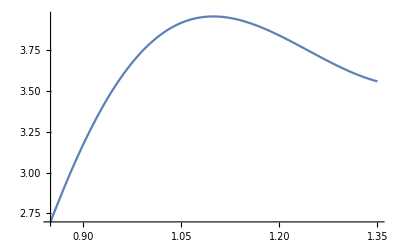

```mathematica
Plot[%160,{x,0.85,1.35}]
```